```mathematica
ReleaseHold[NotebookImport[NotebookDirectory[]<>"AllMatrices.nb","Input"]];
H1
H1//MatrixForm
```

{{m1+m2+mb,0,0,0,0},{0,m1+m2+mb,0,0,0},{0,0,1/(12 (m1+m2+mb))(l1^2 m1^2+4 l1^2 m1 m2+4 l2^2 m1 m2+l2^2 m2^2+4 l1^2 m1 mb+12 l1^2 m2 mb+4 l2^2 m2 mb+12 Ib (m1+m2+mb)+6 l1 l2 m2 (m1+2 mb) Cos[q2]),1/(12 (m1+m2+mb))(l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2]),(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))},{0,0,1/(12 (m1+m2+mb))(l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2]),1/(12 (m1+m2+mb))(l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2]),(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))},{0,0,(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)),(l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)),(l2^2 m2 (4 m1+m2+4 mb))/(12 (m1+m2+mb))}}

(m1+m2+mb | 0 | 0 | 0 | 0
0 | m1+m2+mb | 0 | 0 | 0
0 | 0 | (l1^2 m1^2+4 l1^2 m1 m2+4 l2^2 m1 m2+l2^2 m2^2+4 l1^2 m1 mb+12 l1^2 m2 mb+4 l2^2 m2 mb+12 Ib (m1+m2+mb)+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))
0 | 0 | (l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2^2 m2 (4 m1+m2+4 mb)+l1^2 (m1^2+12 m2 mb+4 m1 (m2+mb))+6 l1 l2 m2 (m1+2 mb) Cos[q2])/(12 (m1+m2+mb)) | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb))
0 | 0 | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)) | (l2 m2 (l2 (4 m1+m2+4 mb)+3 l1 (m1+2 mb) Cos[q2]))/(12 (m1+m2+mb)) | (l2^2 m2 (4 m1+m2+4 mb))/(12 (m1+m2+mb)))

```mathematica
Csc[ⅈ ]//N
```

0.-0.850918 ⅈ

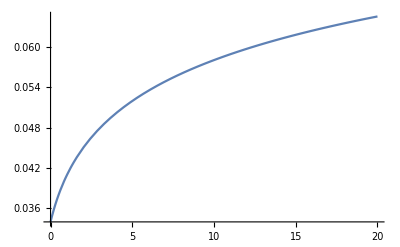

```mathematica
a=0.01;
b=30;
c=1;
Plot [a*Log[b*(c+t)],{t,0,20}]
```